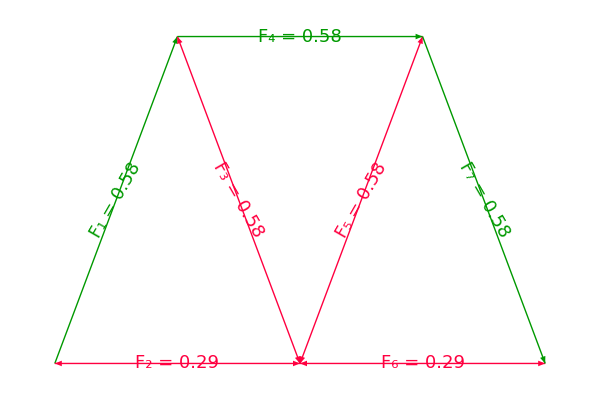

```mathematica
Module[{w,h,θ,Fy,sol,RAx,RAy,RE,F1,F2,F3,F4,F5,F6,F7,colC,colT,p1,p2,p3},
w=1;h=w/2*Tan[θ];θ=60°;Fy=1;

sol=Quiet@Solve[N@{
(*reactions*)rax==0,w*Fy-2*w*re==0,ray-Fy+re==0,
(*A*)f1*Sin[θ]+ray==0,f1*Cos[θ]+f2==0,
(*B*)-f1*Sin[θ]-f3*Sin[θ]==0,-f1*Cos[θ]+f3*Cos[θ]+f4==0,
(*C*)f3*Sin[θ]+f5*Sin[θ]-Fy==0,-f2-f3*Cos[θ]+f5*Cos[θ]+f6==0,
(*D*)-f5*Sin[θ]-f7*Sin[θ]==0
},{rax,ray,re,f1,f2,f3,f4,f5,f6,f7}][[1]];
RAx=rax/.sol;RAy=ray/.sol;RE=re/.sol;
F1=f1/.sol;F2=f2/.sol;F3=f3/.sol;F4=f4/.sol;
F5=f5/.sol;F6=f6/.sol;F7=f7/.sol;

colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

Graphics[{Thick,
Flatten@{If[#1<0,{colC,Arrowheads@{{0.045,0.325},{-0.045,0.675}}},{colT,Arrowheads@{-0.045,0.045}}],#3,
Text[Rotate[Style[Row@{Subscript[Style[" F",Italic],#2]," = ",NumberForm[Abs@#1,{4,2}]," "},18,Background->White],#5],#4]}&@@@{
{F1,1,Arrow[{{0,0},{0.5*w,h}}],{0.25*w,0.5*h},θ},{F2,2,Arrow[{{0,0},{w,0}}],{0.5*w,0},0},{F3,3,Arrow[{{0.5*w,h},{w,0}}],{0.75*w,0.5*h},-θ},{F4,4,Arrow[{{0.5*w,h},{1.5*w,h}}],{w,h},0},{F5,5,Arrow[{{w,0},{1.5*w,h}}],{1.25*w,0.5*h},θ},{F6,6,Arrow[{{w,0},{2*w,0}}],{1.5*w,0},0},{F7,7,Arrow[{{1.5*w,h},{2*w,0}}],{1.75*w,0.5*h},-θ}}
},ImageSize->{600,400}]
]
```

```mathematica
Manipulate[
Module[{w,h,θ,Fy,sol,RAx,RAy,RE,colC,colT,p1,p2,p3},
w=1;h=w/2*Tan[θ];θ=60°;Fy=1;

sol=Quiet@Solve[N@{rax==0,w*Fy-2*w*re==0,ray-Fy+re==0},{rax,ray,re}][[1]];
RAx=rax/.sol;RAy=ray/.sol;RE=re/.sol;

colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

p1=Graphics[{Thick,
{Arrowheads@{{0.05,0.325},{-0.05,0.675}},
Arrow[{{0,0},{0.5*w,h}}],Arrow[{{0.5*w,h},{1.5*w,h}}],Arrow[{{1.5*w,h},{2*w,0}}]},
{Arrowheads@{-0.05,0.05},
Arrow[{{0,0},{w,0}}],Arrow[{{0.5*w,h},{w,0}}],Arrow[{{w,0},{1.5*w,h}}],Arrow[{{w,0},{2*w,0}}]}
}];

p2=Graphics[{Thick,
{Arrowheads@{{0.05,0.325},{-0.05,0.675}},
Arrow[{{0,0},{0.5*w,h}}],Arrow[{{0.5*w,h},{1.5*w,h}}],Arrow[{{1.5*w,h},{2*w,0}}],
Arrow[{{0,0},{w,0}}],Arrow[{{0.5*w,h},{w,0}}],Arrow[{{w,0},{1.5*w,h}}],Arrow[{{w,0},{2*w,0}}]}
}];

p3=Graphics[{
Text[Framed[Style[Subscript[Style["F",Italic],#1],18],Background->White,FrameStyle->None,FrameMargins->Tiny],#2]&@@@{
{1,{0.25*w,0.5*h}},{2,{0.5*w,0}},{3,{0.75*w,0.5*h}},{4,{w,h}},{5,{1.25*w,0.5*h}},{6,{1.5*w,0}},{7,{1.75*w,0.5*h}}},

Text[Framed[Style[Row@{" ",#1," "},18],RoundingRadius->15],#2,#3]&@@@{
{"A",{0,0},{1.5,0}},{"B",{0.5*w,h},{1,-1}},{"C",{w,0},{0,1.5}},{"D",{1.5*w,h},{-1,-1}},{"E",{2*w,0},{-1.5,0}}}
}];

Show[If[TA==1,p1,p2],p3,ImageSize->{600,400}]
],
Control[{{TA,1,""},{1->" solution ",2->" compression "},Setter}]
]
```

```mathematica
(*{Blue,Arrow[{{#*w,-0.25*h},{#*w,0}}]&/@{0,2},Arrow[{{w,-0.5*h},{w,0}}],
Text[Style[Row@{Subscript[Style["R",Italic],#1]," = ",NumberForm[#2,{3,1}]," kN"},18],{#3*w,-0.25*h},{0,1.5}]&@@@{{"A",RAy,0},{"E",RE,2}},
Text[Style[Row@{Subscript[Style["F",Italic],"y"]," = ",NumberForm[Fy,{3,1}]," kN"},18],{w,-0.5*h},{0,1.5}]},

Text[Framed[Style[Subscript[Style["F",Italic],#1],18],Background->White,FrameStyle->None,FrameMargins->Tiny],#2]&@@@{
{1,{0.25*w,0.5*h}},{2,{0.5*w,0}},{3,{0.75*w,0.5*h}},{4,{w,h}},{5,{1.25*w,0.5*h}},{6,{1.5*w,0}},{7,{1.75*w,0.5*h}}}*)
```